## Ver2 (nx x ny data in two columns)

```mathematica
$Version
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];(*Mathematica file in the proper location*)
filename=FileBaseName[NotebookFileName[]];
```

12.3.0 for Mac OS X x86 (64-bit) (May 10, 2021)

-Graphics-

### a. Data import and function def.

#### 0. Data information

```mathematica
Lx=1200;(*um-scanned area *)
Ly=100;(*um-scanned area *)
dx=5;(*step distance*)
dy=20;(*step distance*)
nx=Lx/dx+1;(*sample per line*)
ny=Ly/dy+1(*sample per line*)
```

6

#### 1. Data import

```mathematica
allFiles=FileNames["*.txt"];
```

```mathematica
Print["Imported file names: ",allFiles]
allData=Import[#,"Data"]&/@allFiles;
allData//Dimensions
ndataset=Length[allFiles]
labels=FileBaseName/@allFiles
```

Imported file names: {as26.txt,as27.txt,as28.txt,as29.txt,as30.txt,as31.txt,as32.txt,as33.txt,as34.txt,as35.txt,as36.txt,as37.txt,as38.txt,as39.txt,as40.txt,as41.txt,as42.txt,as43.txt,as44.txt}

{19,1468}

19

{as26,as27,as28,as29,as30,as31,as32,as33,as34,as35,as36,as37,as38,as39,as40,as41,as42,as43,as44}

#### 2. Data process &

```mathematica
cleaning[data_]:=Module[{start,drop1,dt},
start=FirstPosition[data,s_/;StringContainsQ[ToString[s],"Point Cloud:"]];
drop1=Drop[data,start[[1]]+1];
If[StringMatchQ[ToString[drop1[[1]]],"X\tY\tZ"],drop1=Rest[drop1],"error: no XYZ identified"];
dt=Interpreter["Number"]/@StringSplit[#,"\t"]&/@drop1;(*function &/@ list -> & means "this is a function." *)
dt];
```

```mathematica
StringSplit["x y z"](*any space and tabs*)
StringSplit["x y z","\t"](*only tabs*)
StringSplit["x x2\ty\tz","\t"](*only tabs*)
```

{x,y,z}

{x y z}

{x x2,y,z}

```mathematica
Interpreter["Number"]/@{"0","50","1.23e-11"}
%[[3]]*10^9
```

{0,50,1.23×10^-11}

0.0123

```mathematica
cleanedData=cleaning/@allData;
cleanedData//Dimensions
```

{19,1446,3}

```mathematica
zMat=ArrayReshape[#*10^9,{ny,nx}]&/@(#[[All,3]]&/@cleanedData);
zMat//Dimensions
zMat[[1]]//Dimensions
zMat[[1]]//MatrixForm
```

{19,6,241}

{6,241}

(0.922602 | 0.918811 | 0.919443 | 0.938394 | 0.93713 | 0.941552 | 0.947238 | 0.961767 | 0.971874 | 0.978191 | 0.995879 | 1.00599 | 1.00978 | 1.0382 | 1.05589 | 1.06221 | 1.07547 | 1.09379 | 1.11906 | 1.13359 | 1.15128 | 1.15633 | 1.17339 | 1.17907 | 1.1797 | 1.19423 | 1.19171 | 1.19676 | 1.21697 | 1.21192 | 1.17149 | 1.08811 | 1.0123 | 0.884068 | 0.798156 | 0.72551 | 0.696452 | 0.702769 | 0.677501 | 0.679396 | 0.686345 | 0.674342 | 0.693925 | 0.700242 | 0.698347 | 0.716666 | 0.705927 | 0.69582 | 0.697715 | 0.697084 | 0.688871 | 0.683818 | 0.674342 | 0.686345 | 0.671184 | 0.668657 | 0.662972 | 0.653496 | 0.646547 | 0.651601 | 0.625701 | 0.633282 | 0.626333 | 0.620016 | 0.64023 | 0.617489 | 0.639599 | 0.639599 | 0.654128 | 0.654128 | 0.649074 | 0.650338 | 0.644021 | 0.657918 | 0.661708 | 0.644021 | 0.64023 | 0.647811 | 0.637704 | 0.650338 | 0.660445 | 0.66992 | 0.644021 | 0.66613 | 0.666762 | 0.674974 | 0.666762 | 0.673711 | 0.682554 | 0.673711 | 0.672447 | 0.673711 | 0.678764 | 0.688871 | 0.693925 | 0.676237 | 0.690135 | 0.698979 | 0.702769 | 0.707823 | 0.704664 | 0.69582 | 0.691398 | 0.695189 | 0.718561 | 0.704032 | 0.692662 | 0.700874 | 0.712876 | 0.712876 | 0.71414 | 0.709718 | 0.724247 | 0.709718 | 0.738776 | 0.7293 | 0.733091 | 0.709086 | 0.718561 | 0.727405 | 0.724247 | 0.733091 | 0.72172 | 0.728037 | 0.729932 | 0.72172 | 0.745093 | 0.738144 | 0.741935 | 0.727405 | 0.736249 | 0.750147 | 0.738144 | 0.738776 | 0.741303 | 0.75899 | 0.741303 | 0.733091 | 0.740039 | 0.75141 | 0.754569 | 0.753305 | 0.746988 | 0.757727 | 0.768466 | 0.767202 | 0.749515 | 0.753305 | 0.768466 | 0.760885 | 0.776678 | 0.761517 | 0.767202 | 0.764044 | 0.783627 | 0.781732 | 0.774783 | 0.785522 | 0.788049 | 0.78868 | 0.796261 | 0.805105 | 0.810158 | 0.812685 | 0.801946 | 0.831005 | 0.822161 | 0.828478 | 0.861326 | 0.881541 | 0.868907 | 0.86638 | 0.880909 | 0.892911 | 0.903019 | 0.927023 | 0.949133 | 0.954186 | 0.970611 | 0.983876 | 1.01104 | 1.03568 | 1.05652 | 1.0641 | 1.0919 | 1.10453 | 1.11717 | 1.12727 | 1.10832 | 1.11338 | 1.11274 | 1.09506 | 1.09506 | 1.09821 | 1.09253 | 1.09569 | 1.066 | 1.05589 | 1.04642 | 1.04073 | 1.05021 | 1.02746 | 1.03568 | 1.04389 | 1.01041 | 1.00788 | 0.993352 | 1.01483 | 0.997774 | 1.00156 | 1.01104 | 0.987667 | 0.983876 | 0.99272 | 0.968716 | 0.977559 | 0.969979 | 0.975033 | 0.975033 | 0.957977 | 0.957345 | 0.949133 | 0.958608 | 0.95166 | 0.952291 | 0.939657 | 0.957977 | 0.947238 | 0.947238 | 0.939657 | 0.928918 | 0.939657 | 0.935867 | 0.93713 | 0.940921 | 0.920075 | 0.916284 | 0.921338 | 0.92197 | 0.916916 | 0.908704
0.920075 | 0.936499 | 0.953555 | 0.954818 | 0.95166 | 0.95545 | 0.987035 | 0.954818 | 1.00093 | 0.967452 | 0.994615 | 1.01736 | 1.02241 | 1.03252 | 1.04578 | 1.0382 | 1.08558 | 1.08369 | 1.12538 | 1.12601 | 1.12917 | 1.14875 | 1.16518 | 1.1816 | 1.19739 | 1.20434 | 1.21255 | 1.23719 | 1.22961 | 1.24414 | 1.25235 | 1.23214 | 1.1538 | 1.05779 | 0.946606 | 0.86259 | 0.805105 | 0.774151 | 0.770361 | 0.757727 | 0.762781 | 0.745093 | 0.762149 | 0.765307 | 0.753305 | 0.736881 | 0.726774 | 0.714771 | 0.726142 | 0.712245 | 0.709086 | 0.698979 | 0.686345 | 0.677501 | 0.690767 | 0.68445 | 0.669289 | 0.66234 | 0.657286 | 0.653496 | 0.647811 | 0.649074 | 0.645916 | 0.635177 | 0.644021 | 0.657286 | 0.649706 | 0.651601 | 0.655391 | 0.656023 | 0.659181 | 0.653496 | 0.651601 | 0.642757 | 0.649074 | 0.64023 | 0.63644 | 0.635808 | 0.634545 | 0.642126 | 0.652233 | 0.668657 | 0.662972 | 0.656023 | 0.66613 | 0.661708 | 0.66992 | 0.66613 | 0.661077 | 0.678764 | 0.681291 | 0.673079 | 0.676237 | 0.678764 | 0.694557 | 0.683186 | 0.709718 | 0.704664 | 0.68824 | 0.717298 | 0.706559 | 0.722983 | 0.704664 | 0.706559 | 0.676869 | 0.709086 | 0.709086 | 0.688871 | 0.714771 | 0.699611 | 0.706559 | 0.709086 | 0.709718 | 0.719825 | 0.721088 | 0.712245 | 0.71793 | 0.719193 | 0.724247 | 0.726774 | 0.727405 | 0.727405 | 0.728037 | 0.735617 | 0.734986 | 0.736881 | 0.745725 | 0.750147 | 0.740039 | 0.740039 | 0.749515 | 0.749515 | 0.752042 | 0.752673 | 0.746988 | 0.741303 | 0.7552 | 0.764676 | 0.765307 | 0.760254 | 0.770361 | 0.767834 | 0.760254 | 0.771625 | 0.771625 | 0.767202 | 0.776678 | 0.775415 | 0.785522 | 0.7811 | 0.780468 | 0.785522 | 0.78868 | 0.794997 | 0.780468 | 0.800051 | 0.800683 | 0.800051 | 0.815844 | 0.805105 | 0.808895 | 0.813317 | 0.820897 | 0.834795 | 0.827846 | 0.84048 | 0.848692 | 0.856904 | 0.857536 | 0.876487 | 0.882804 | 0.885963 | 0.901755 | 0.920075 | 0.928918 | 0.949133 | 0.954186 | 0.978823 | 0.99272 | 1.02746 | 1.03631 | 1.05905 | 1.08811 | 1.102 | 1.11843 | 1.13864 | 1.1538 | 1.14875 | 1.15191 | 1.15065 | 1.13422 | 1.13233 | 1.12664 | 1.13296 | 1.11148 | 1.10516 | 1.09569 | 1.09758 | 1.09695 | 1.08937 | 1.07547 | 1.0799 | 1.05652 | 1.07926 | 1.06347 | 1.04578 | 1.078 | 1.02746 | 1.02052 | 1.00346 | 1.03252 | 1.0123 | 1.00599 | 1.0281 | 0.99272 | 1.00599 | 1.00156 | 0.999669 | 0.999037 | 1.00725 | 0.996511 | 0.976928 | 0.971874 | 0.990193 | 0.971243 | 0.962399 | 0.960504 | 0.947869 | 0.953555 | 0.954818 | 0.960504 | 0.958608 | 0.948501 | 0.947869 | 0.943448 | 0.939026 | 0.946606 | 0.943448 | 0.927023 | 0.932709 | 0.939657
0.939026 | 0.969347 | 0.939657 | 0.956713 | 0.961767 | 0.949133 | 0.990825 | 0.983876 | 0.997774 | 1.0022 | 1.01104 | 1.02178 | 1.0401 | 1.04326 | 1.05463 | 1.06852 | 1.08369 | 1.08558 | 1.13422 | 1.1538 | 1.1557 | 1.16012 | 1.19929 | 1.18918 | 1.20434 | 1.21508 | 1.22519 | 1.24035 | 1.24982 | 1.22645 | 1.19423 | 1.16138 | 1.08874 | 0.995879 | 0.916284 | 0.852482 | 0.81079 | 0.798156 | 0.78489 | 0.799419 | 0.781732 | 0.7811 | 0.781732 | 0.762149 | 0.763412 | 0.75899 | 0.748883 | 0.740039 | 0.731196 | 0.721088 | 0.71793 | 0.711613 | 0.705927 | 0.678133 | 0.673711 | 0.678764 | 0.655391 | 0.663603 | 0.651601 | 0.637704 | 0.643389 | 0.669289 | 0.661077 | 0.65855 | 0.653496 | 0.661077 | 0.66992 | 0.664235 | 0.661708 | 0.648443 | 0.649706 | 0.641494 | 0.645916 | 0.644021 | 0.647811 | 0.671184 | 0.661708 | 0.669289 | 0.668657 | 0.665499 | 0.680659 | 0.656023 | 0.653496 | 0.678133 | 0.668025 | 0.668657 | 0.669289 | 0.66613 | 0.679396 | 0.68824 | 0.692662 | 0.682554 | 0.681923 | 0.679396 | 0.69582 | 0.704032 | 0.69203 | 0.694557 | 0.713508 | 0.700874 | 0.71414 | 0.702769 | 0.717298 | 0.736249 | 0.722983 | 0.724247 | 0.738144 | 0.738776 | 0.722983 | 0.727405 | 0.724247 | 0.724247 | 0.716666 | 0.738144 | 0.726142 | 0.7293 | 0.726774 | 0.752042 | 0.729932 | 0.728037 | 0.735617 | 0.734986 | 0.736881 | 0.7552 | 0.758359 | 0.756464 | 0.75141 | 0.746988 | 0.757727 | 0.760254 | 0.754569 | 0.746988 | 0.752042 | 0.764044 | 0.764676 | 0.757727 | 0.772256 | 0.767202 | 0.777942 | 0.77731 | 0.780468 | 0.77352 | 0.778573 | 0.787417 | 0.772888 | 0.7811 | 0.776678 | 0.777942 | 0.784259 | 0.778573 | 0.795629 | 0.789944 | 0.798788 | 0.789944 | 0.797524 | 0.796261 | 0.808895 | 0.807631 | 0.825951 | 0.803841 | 0.825951 | 0.819002 | 0.834795 | 0.823424 | 0.833531 | 0.845534 | 0.849956 | 0.845534 | 0.857536 | 0.873329 | 0.881541 | 0.908704 | 0.904914 | 0.914389 | 0.923865 | 0.950396 | 0.957345 | 0.971874 | 0.995247 | 1.00978 | 1.04452 | 1.06031 | 1.0799 | 1.10895 | 1.12854 | 1.15317 | 1.16454 | 1.17907 | 1.18476 | 1.16391 | 1.1696 | 1.16328 | 1.1538 | 1.1437 | 1.13864 | 1.14307 | 1.11338 | 1.11148 | 1.10516 | 1.09569 | 1.08621 | 1.09063 | 1.09127 | 1.06347 | 1.07105 | 1.0641 | 1.06916 | 1.04452 | 1.03441 | 1.04642 | 1.03441 | 1.03631 | 1.01736 | 1.02999 | 1.00535 | 1.00914 | 1.00978 | 1.0142 | 0.995879 | 0.989562 | 0.997142 | 0.997142 | 0.984508 | 0.990193 | 0.988299 | 0.980718 | 0.969979 | 0.972506 | 0.969347 | 0.961135 | 0.971874 | 0.956713 | 0.961135 | 0.956713 | 0.952291 | 0.949765 | 0.943448 | 0.954818 | 0.939657 | 0.933972 | 0.923865
0.977559 | 0.981981 | 0.981981 | 0.983876 | 0.990825 | 1.00725 | 1.00725 | 1.01988 | 1.01609 | 1.01736 | 1.03252 | 1.05968 | 1.0641 | 1.0641 | 1.08369 | 1.09821 | 1.12159 | 1.12854 | 1.15001 | 1.16644 | 1.1936 | 1.20181 | 1.22392 | 1.25109 | 1.24351 | 1.27004 | 1.29341 | 1.29846 | 1.30478 | 1.29215 | 1.26309 | 1.2214 | 1.17465 | 1.1298 | 1.054 | 0.993984 | 0.963662 | 0.922602 | 0.896702 | 0.872065 | 0.84048 | 0.821529 | 0.811422 | 0.789312 | 0.776046 | 0.768466 | 0.750778 | 0.738776 | 0.724247 | 0.696452 | 0.683818 | 0.68445 | 0.664235 | 0.645916 | 0.649074 | 0.649706 | 0.649074 | 0.656655 | 0.664867 | 0.65855 | 0.665499 | 0.664867 | 0.68445 | 0.683186 | 0.688871 | 0.679396 | 0.678764 | 0.687608 | 0.680028 | 0.66613 | 0.668657 | 0.674342 | 0.683186 | 0.690135 | 0.692662 | 0.681923 | 0.683818 | 0.698979 | 0.691398 | 0.69203 | 0.699611 | 0.694557 | 0.707191 | 0.712245 | 0.717298 | 0.724879 | 0.727405 | 0.746988 | 0.749515 | 0.748883 | 0.754569 | 0.74762 | 0.764676 | 0.757095 | 0.757727 | 0.75899 | 0.783627 | 0.764676 | 0.77352 | 0.774783 | 0.77731 | 0.780468 | 0.776046 | 0.78489 | 0.77731 | 0.772256 | 0.7811 | 0.770361 | 0.775415 | 0.771625 | 0.77352 | 0.772256 | 0.764044 | 0.757727 | 0.761517 | 0.760254 | 0.764676 | 0.767202 | 0.763412 | 0.768466 | 0.767202 | 0.77352 | 0.772888 | 0.779205 | 0.786785 | 0.793103 | 0.781732 | 0.789944 | 0.808895 | 0.790576 | 0.785522 | 0.793734 | 0.789312 | 0.791839 | 0.806368 | 0.80321 | 0.794997 | 0.800683 | 0.807631 | 0.813949 | 0.815844 | 0.808895 | 0.817739 | 0.824688 | 0.815212 | 0.81079 | 0.819634 | 0.808263 | 0.820266 | 0.836058 | 0.812685 | 0.817739 | 0.836058 | 0.8329 | 0.829741 | 0.836058 | 0.839217 | 0.838585 | 0.845534 | 0.848061 | 0.863853 | 0.865748 | 0.84427 | 0.867643 | 0.867643 | 0.879014 | 0.884699 | 0.89607 | 0.884699 | 0.896702 | 0.909336 | 0.930814 | 0.938394 | 0.942816 | 0.965557 | 0.981981 | 0.997142 | 1.00535 | 1.02431 | 1.03883 | 1.07863 | 1.08495 | 1.09885 | 1.12348 | 1.14559 | 1.15886 | 1.20371 | 1.20813 | 1.20939 | 1.23214 | 1.23466 | 1.22013 | 1.21129 | 1.20939 | 1.19171 | 1.18792 | 1.18223 | 1.17781 | 1.17149 | 1.15886 | 1.13801 | 1.13928 | 1.13422 | 1.12601 | 1.12096 | 1.1039 | 1.10516 | 1.09948 | 1.09063 | 1.08558 | 1.08116 | 1.08495 | 1.07674 | 1.0641 | 1.06221 | 1.06094 | 1.05968 | 1.04957 | 1.05463 | 1.04452 | 1.0281 | 1.03694 | 1.03504 | 1.04262 | 1.02052 | 1.01925 | 1.03441 | 1.01167 | 1.00788 | 1.00283 | 1.00409 | 1.00472 | 1.00283 | 0.997774 | 1.00472 | 0.997142 | 0.999037 | 0.984508 | 0.987035 | 0.980718 | 0.977559
1.03441 | 1.03947 | 1.03883 | 1.04578 | 1.05336 | 1.05715 | 1.06473 | 1.07484 | 1.06473 | 1.08874 | 1.09316 | 1.09885 | 1.11843 | 1.1437 | 1.13928 | 1.15444 | 1.16518 | 1.19297 | 1.20308 | 1.23214 | 1.24287 | 1.26562 | 1.30289 | 1.3111 | 1.3351 | 1.34521 | 1.36353 | 1.37995 | 1.38185 | 1.37174 | 1.35469 | 1.32247 | 1.27446 | 1.22835 | 1.16581 | 1.11022 | 1.07547 | 1.0281 | 0.985771 | 0.933972 | 0.911862 | 0.874592 | 0.853114 | 0.8329 | 0.786785 | 0.770361 | 0.74383 | 0.719193 | 0.68445 | 0.659181 | 0.644021 | 0.63644 | 0.639599 | 0.637704 | 0.639599 | 0.648443 | 0.659813 | 0.676237 | 0.673711 | 0.674974 | 0.674974 | 0.678764 | 0.686976 | 0.675606 | 0.673711 | 0.672447 | 0.645916 | 0.651601 | 0.652865 | 0.66234 | 0.671184 | 0.681291 | 0.705927 | 0.704664 | 0.710349 | 0.716666 | 0.721088 | 0.740671 | 0.741303 | 0.753305 | 0.765307 | 0.769729 | 0.769098 | 0.779837 | 0.775415 | 0.77352 | 0.772256 | 0.779837 | 0.778573 | 0.772888 | 0.786785 | 0.779837 | 0.790576 | 0.813317 | 0.810158 | 0.809527 | 0.812054 | 0.81079 | 0.815212 | 0.829109 | 0.817739 | 0.81458 | 0.801315 | 0.80321 | 0.785522 | 0.794997 | 0.785522 | 0.792471 | 0.774783 | 0.772256 | 0.774783 | 0.767202 | 0.783627 | 0.771625 | 0.784259 | 0.781732 | 0.789312 | 0.795629 | 0.786154 | 0.792471 | 0.788049 | 0.792471 | 0.791207 | 0.793103 | 0.798788 | 0.805736 | 0.799419 | 0.803841 | 0.799419 | 0.805105 | 0.825319 | 0.810158 | 0.807631 | 0.81079 | 0.820897 | 0.829741 | 0.829109 | 0.815844 | 0.838585 | 0.831005 | 0.829109 | 0.841112 | 0.8329 | 0.828478 | 0.830373 | 0.855641 | 0.841743 | 0.837322 | 0.84048 | 0.843639 | 0.846165 | 0.852482 | 0.852482 | 0.869538 | 0.868275 | 0.861326 | 0.867643 | 0.876487 | 0.865748 | 0.885963 | 0.880277 | 0.884068 | 0.891648 | 0.891016 | 0.89607 | 0.913758 | 0.920075 | 0.932077 | 0.934604 | 0.92955 | 0.947238 | 0.952291 | 0.971243 | 0.989562 | 1.00851 | 1.0262 | 1.03441 | 1.05526 | 1.066 | 1.07863 | 1.09758 | 1.13549 | 1.15444 | 1.16265 | 1.1816 | 1.21192 | 1.24414 | 1.24793 | 1.26498 | 1.25993 | 1.27004 | 1.27256 | 1.27888 | 1.26372 | 1.25551 | 1.2473 | 1.24414 | 1.23593 | 1.21192 | 1.21382 | 1.19992 | 1.20939 | 1.18602 | 1.18539 | 1.17781 | 1.1677 | 1.16391 | 1.15949 | 1.15001 | 1.14875 | 1.13296 | 1.12348 | 1.13612 | 1.11969 | 1.12096 | 1.12917 | 1.11969 | 1.10137 | 1.11211 | 1.09253 | 1.09127 | 1.08874 | 1.08684 | 1.08811 | 1.07484 | 1.08621 | 1.07168 | 1.05842 | 1.07042 | 1.04831 | 1.05652 | 1.05021 | 1.04326 | 1.05526 | 1.04578 | 1.03757 | 1.03315 | 1.03189 | 1.02746 | 1.04136 | 1.03568
1.27256 | 1.27256 | 1.28204 | 1.2852 | 1.29467 | 1.28583 | 1.29531 | 1.29594 | 1.30857 | 1.31805 | 1.31868 | 1.31931 | 1.33005 | 1.34647 | 1.36858 | 1.37364 | 1.38817 | 1.40649 | 1.43428 | 1.43681 | 1.46018 | 1.47913 | 1.49492 | 1.51261 | 1.5562 | 1.54483 | 1.56252 | 1.596 | 1.58273 | 1.60105 | 1.5802 | 1.55304 | 1.48671 | 1.39764 | 1.27888 | 1.15444 | 1.04578 | 0.960504 | 0.873329 | 0.827214 | 0.759622 | 0.719825 | 0.68445 | 0.655391 | 0.623174 | 0.592853 | 0.544212 | 0.525892 | 0.539158 | 0.537263 | 0.552424 | 0.56948 | 0.57706 | 0.597275 | 0.620016 | 0.62886 | 0.654759 | 0.659181 | 0.656023 | 0.672447 | 0.659181 | 0.654759 | 0.656023 | 0.640862 | 0.652233 | 0.654128 | 0.668025 | 0.687608 | 0.69582 | 0.720457 | 0.733091 | 0.732459 | 0.740039 | 0.731827 | 0.745093 | 0.746988 | 0.764676 | 0.764044 | 0.774783 | 0.794997 | 0.792471 | 0.788049 | 0.783627 | 0.785522 | 0.792471 | 0.789312 | 0.792471 | 0.779837 | 0.78489 | 0.787417 | 0.791839 | 0.805736 | 0.81079 | 0.829109 | 0.834163 | 0.837322 | 0.839848 | 0.839848 | 0.84048 | 0.842375 | 0.826582 | 0.824688 | 0.805736 | 0.815844 | 0.829109 | 0.822793 | 0.829109 | 0.821529 | 0.823424 | 0.829741 | 0.835427 | 0.845534 | 0.854378 | 0.843007 | 0.846165 | 0.855641 | 0.868275 | 0.865117 | 0.857536 | 0.860695 | 0.894806 | 0.886594 | 0.891648 | 0.879014 | 0.880277 | 0.897965 | 0.904914 | 0.906809 | 0.899228 | 0.900492 | 0.911862 | 0.918811 | 0.915021 | 0.912494 | 0.920075 | 0.916916 | 0.91818 | 0.932709 | 0.928918 | 0.921338 | 0.930182 | 0.932077 | 0.950396 | 0.933341 | 0.933972 | 0.936499 | 0.945342 | 0.936499 | 0.964294 | 0.95545 | 0.949133 | 0.964926 | 0.971243 | 0.963662 | 0.95924 | 0.969979 | 0.987667 | 0.974401 | 0.979455 | 0.986403 | 0.987035 | 0.986403 | 1.0003 | 1.00978 | 1.0022 | 1.00472 | 1.01483 | 1.03631 | 1.02304 | 1.04515 | 1.05652 | 1.06094 | 1.07168 | 1.09695 | 1.10137 | 1.12348 | 1.12475 | 1.17339 | 1.1677 | 1.18918 | 1.21066 | 1.23214 | 1.25677 | 1.28141 | 1.3092 | 1.32247 | 1.34774 | 1.36479 | 1.37806 | 1.39006 | 1.38501 | 1.37553 | 1.3768 | 1.37111 | 1.36795 | 1.34395 | 1.33826 | 1.32436 | 1.32373 | 1.30731 | 1.30099 | 1.29404 | 1.29215 | 1.26688 | 1.27256 | 1.26688 | 1.24477 | 1.24414 | 1.23214 | 1.22392 | 1.21192 | 1.22329 | 1.2075 | 1.20624 | 1.20371 | 1.19676 | 1.18476 | 1.19423 | 1.17212 | 1.16644 | 1.15823 | 1.14938 | 1.14875 | 1.15191 | 1.15317 | 1.1418 | 1.13801 | 1.13864 | 1.13169 | 1.12601 | 1.12475 | 1.11906 | 1.11843 | 1.10895 | 1.11717 | 1.11717 | 1.11085 | 1.10453 | 1.11148 | 1.09253 | 1.10959)

#### Contour plot_function

```mathematica
tickX=Table[{i,ToString[(i-1)*dx]},{i,1,nx,50}];
tickY=Table[{i,ToString[(i-1)*dy]},{i,1,ny}];
asratio=2;
```

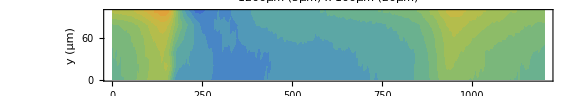

```mathematica
SetAttributes[mapB,HoldFirst];
mapB[temp_,min_,max_,dd_]:=Module[{leg},
leg=Round[Table[i,{i,min,max,(max-min)/dd}],0.001];
ListContourPlot[Evaluate[temp],PlotRange->All,Frame->True,ImageSize->Large,LabelStyle->{FontFamily->"Arial",FontSize->16,Black},
PlotLabel->Row[{Lx,"μm"," (",dx,"μm",") x ",Ly,"μm"," (",dy,"μm",")"}],
FrameLabel->{"x (μm)","y (μm)"},
FrameTicks->{{tickY,None},{tickX,None}},
AspectRatio->Ly/Lx*asratio,
GridLines->{Range[0,Lx,100],Range[0,Ly,10]*(ny-1)/Ly},
Method->{"GridLinesInFront"->True},ColorFunction->Function[{z},ColorData["Rainbow"][Rescale[z,{min,max}]]],ColorFunctionScaling->False,Contours->leg,ContourStyle->None,PlotLegends->Placed[BarLegend[{"Rainbow",{min,max}},LegendMarkerSize->Medium,LegendLabel->"Current (nA)"],{After,Top}]]];
mapB[zMat[[1]],0.1,2,20]
```

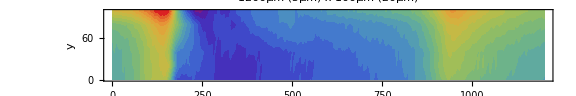

```mathematica
mapA1[temp_,cont_]:=Module[{},
ListContourPlot[temp,PlotRange->All,Frame->True,ImageSize->Large,LabelStyle->{FontFamily->"Arial",FontSize->16,Black},FrameLabel->{"x","y"},FrameTicks->{{tickY,None},{tickX,None}},
AspectRatio->Ly/Lx*asratio,
GridLines->{Range[0,Lx,100],Range[0,Ly,10]*(ny-1)/Ly},
Method->{"GridLinesInFront"->True},
ColorFunction->"Rainbow",Contours->cont,ContourStyle->None,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->Medium,LegendLabel->"Intensity"],{After,Top}],
PlotLabel->Row[{Lx,"μm"," (",dx,"μm",") x ",Ly,"μm"," (",dy,"μm",")"}]]]
mapA1[zMat[[1]],20]
```

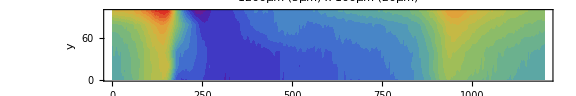

```mathematica
mapA2[temp_,cont_]:=Module[{rr},
rr=Round[Table[i,{i,Min[temp],Max[temp],(Max[temp]-Min[temp])/cont}],0.01];
ListContourPlot[temp,PlotRange->All,Frame->True,ImageSize->Large,LabelStyle->{FontFamily->"Arial",FontSize->16,Black},FrameLabel->{"x","y"},FrameTicks->{{tickY,None},{tickX,None}},
AspectRatio->Ly/Lx*asratio,
GridLines->{Range[0,Lx,100],Range[0,Ly,10]*(ny-1)/Ly},
Method->{"GridLinesInFront"->True},
ColorFunction->"Rainbow",Contours->rr,ContourStyle->None,
PlotLegends->Placed[BarLegend[{ColorData["Rainbow"],{Min[rr],Max[rr]}},LegendMarkerSize->Medium,LegendLabel->"Intensity"],{After,Top}],
PlotLabel->Row[{Lx,"μm"," (",dx,"μm",") x ",Ly,"μm"," (",dy,"μm",")"}]]]
mapA2[zMat[[1]],20]
```

#### Line profiles_function

```mathematica
ClearAll[LPy];
LPy[zMatn_,y_]:=Module[{rowIndex,xvals,lineProfile},
rowIndex=Round[y/dy]+1;
xvals=Range[0,dx*(nx-1),dx];
lineProfile=zMatn[[rowIndex]];
ListLinePlot[Transpose[{xvals,lineProfile}],Frame->True,FrameLabel->{"x (μm)","Current (nA)"},PlotLabel->"Line Profile at y = "<>ToString[y]<>" μm  ",PlotRange->All,PlotStyle->Thick,LabelStyle->{FontFamily->"Arial",FontSize->14},ImageSize->Large]];
```

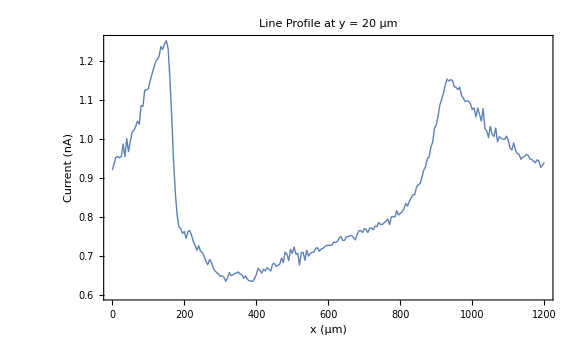

```mathematica
LPy[zMat[[1]],20]
```

#### Line profiles_comparison (need update)

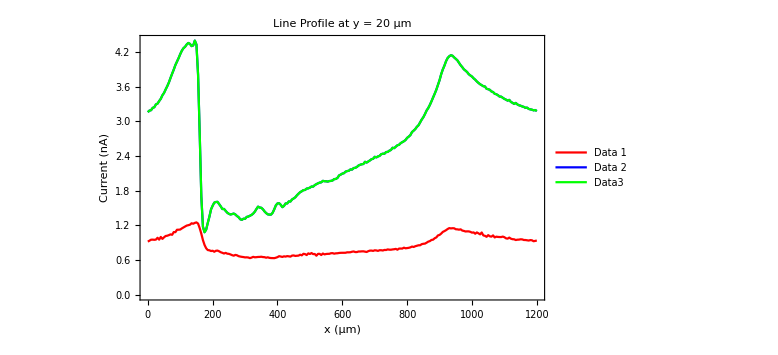

```mathematica
LPyCompare[z1_,z2_,z3_,y_]:=Module[{rowIndex,xvals,curve1,curve2,curve3},
rowIndex=Round[y/dy]+1;
xvals=Range[0,dx*(nx-1),dx];
curve1=Transpose[{xvals,z1[[rowIndex]]}];
curve2=Transpose[{xvals,z2[[rowIndex]]}];
curve3=Transpose[{xvals,z3[[rowIndex]]}];
ListLinePlot[{curve1,curve2,curve3},PlotStyle->{Red,Blue,Green},Frame->True,FrameLabel->{"x (μm)","Current (nA)"},PlotLabel->"Line Profile at y = "<>ToString[y]<>" μm",PlotRange->All,
PlotLegends->Placed[LineLegend[{"Data 1","Data 2","Data3"}],Right],
LabelStyle->{FontFamily->"Arial",FontSize->14},ImageSize->Large]];

LPyCompare[zMat[[1]],zMat[[2]],zMat[[2]],20]
```

#### Line profiles_avg

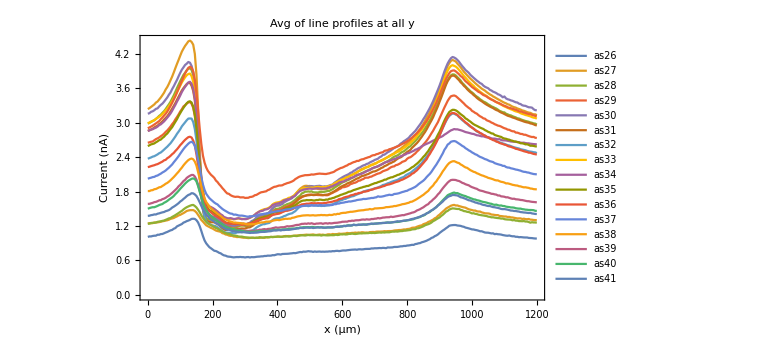

```mathematica
yIndices=Round[Range[0,Ly,dy]/dy]+1;
xvals=Range[0,dx*(nx-1),dx];
avgProf=Table[Thread[{xvals,Mean[zMat[[i,yIndices]]]}],{i,Length[zMat]}];
avgPplots=
ListLinePlot[Table[avgProf[[i]],{i,1,ndataset}],PlotStyle->Automatic,Frame->True,FrameLabel->{"x (μm)","Current (nA)"},PlotLabel->"Avg of line profiles at all y",PlotRange->All,PlotLegends->Placed[LineLegend[labels],Right],
LabelStyle->{FontFamily->"Arial",FontSize->14},ImageSize->Large]
```

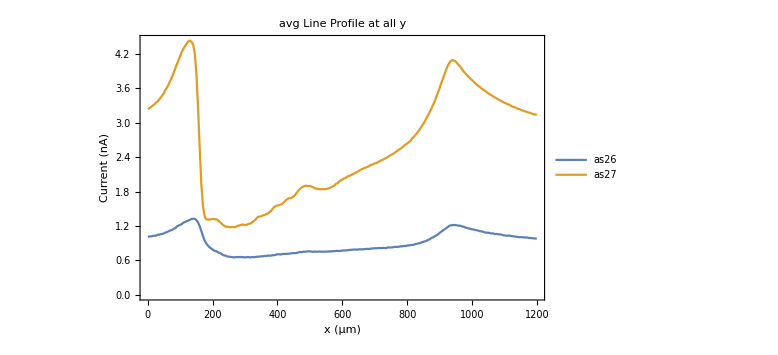

```mathematica
ListLinePlot[{avgProf[[1]],avgProf[[2]]},PlotStyle->Automatic,Frame->True,FrameLabel->{"x (μm)","Current (nA)"},PlotLabel->"avg Line Profile at all y",PlotRange->All,PlotLegends->Placed[LineLegend[labels],Right],
LabelStyle->{FontFamily->"Arial",FontSize->14},ImageSize->Large]
```

## Check

```mathematica
ndataset
```

19

{as26,-Graphics-}

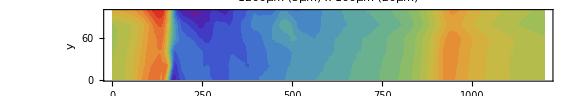
{as27,-Graphics-}

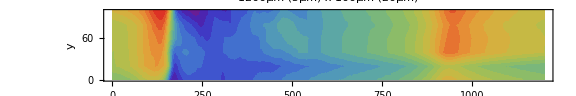
{as28,-Graphics-}

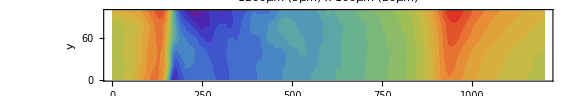
{as29,-Graphics-}

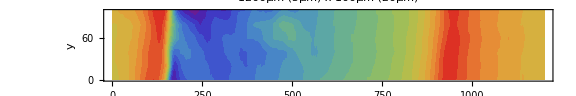
{as30,-Graphics-}

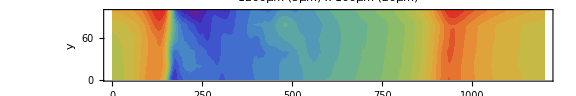
{as31,-Graphics-}

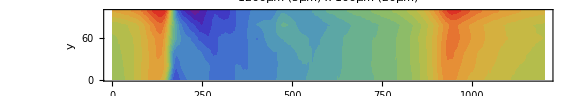
{as32,-Graphics-}

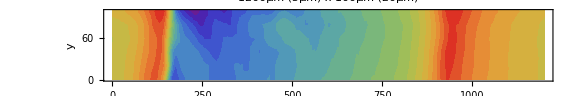
{as33,-Graphics-}

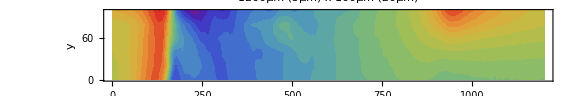
{as34,-Graphics-}

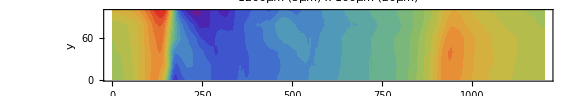
{as35,-Graphics-}

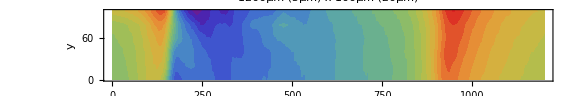
{as36,-Graphics-}

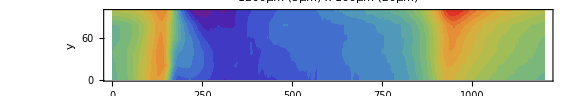
{as37,-Graphics-}

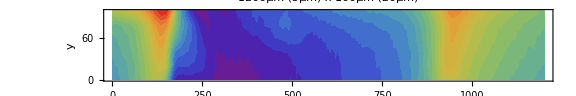
{as38,-Graphics-}

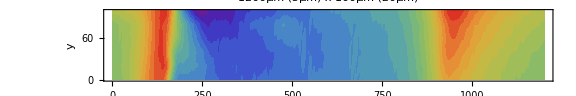
{as39,-Graphics-}

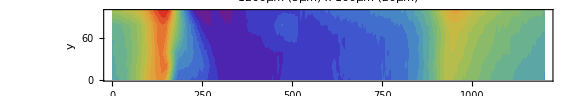
{as40,-Graphics-}

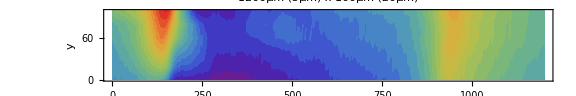
{as41,-Graphics-}

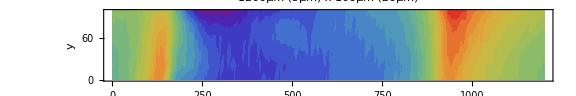
{as42,-Graphics-}

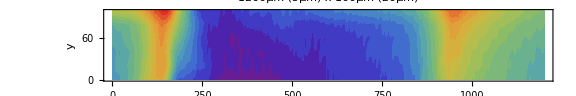
{as43,-Graphics-}

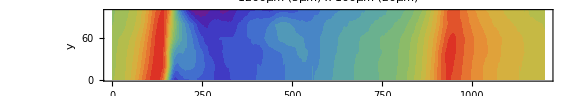
{as44,-Graphics-}

```mathematica
With[{i=1},{labels[[i]],mapA2[zMat[[i]],20]}]
With[{i=2},{labels[[i]],mapA2[zMat[[i]],20]}]
With[{i=3},{labels[[i]],mapA2[zMat[[i]],20]}]
With[{i=4},{labels[[i]],mapA2[zMat[[i]],20]}]
With[{i=5},{labels[[i]],mapA2[zMat[[i]],20]}]

With[{i=6},{labels[[i]],mapA2[zMat[[i]],20]}]
With[{i=7},{labels[[i]],mapA2[zMat[[i]],20]}]
With[{i=8},{labels[[i]],mapA2[zMat[[i]],20]}]
With[{i=9},{labels[[i]],mapA2[zMat[[i]],20]}]
With[{i=10},{labels[[i]],mapA2[zMat[[i]],20]}]

With[{i=11},{labels[[i]],mapA2[zMat[[i]],20]}]
With[{i=12},{labels[[i]],mapA2[zMat[[i]],20]}]
With[{i=13},{labels[[i]],mapA2[zMat[[i]],20]}]
With[{i=14},{labels[[i]],mapA2[zMat[[i]],20]}]
With[{i=15},{labels[[i]],mapA2[zMat[[i]],20]}]
With[{i=16},{labels[[i]],mapA2[zMat[[i]],20]}]
With[{i=17},{labels[[i]],mapA2[zMat[[i]],20]}]
With[{i=18},{labels[[i]],mapA2[zMat[[i]],20]}]
With[{i=19},{labels[[i]],mapA2[zMat[[i]],20]}]
```

```mathematica
Table[LPy[zMat[[1]],i],{i,0,100,20}];
```

```mathematica
Table[LPy[zMat[[i]],20],{i,1,ndataset}];
```

```mathematica
avgPplots
```

-Graphics-

```mathematica
(*
ListLinePlot[{avgProf[[1]],avgProf[[2]],avgProf[[5]],avgProf[[6]],avgProf[[9]]},PlotRange->Full,PlotLegends->{labels[[1]],labels[[2]],labels[[5]],labels[[6]],labels[[9]]},
PlotStyle->Automatic,
Frame->True,
FrameLabel->{"x (μm)","Current (nA)"},
PlotLabel->"avg Line Profile at all y",
LabelStyle->{FontFamily->"Arial",FontSize->14},
ImageSize->Large
]
ListLinePlot[{avgProf[[1]],avgProf[[2]],avgProf[[7]]},PlotRange->{Automatic,{-0.5,20}},PlotLegends->{labels[[1]],labels[[2]],labels[[7]]},
PlotStyle->Automatic,
Frame->True,
FrameLabel->{"x (μm)","Current (nA)"},
PlotLabel->"avg Line Profile at all y",
LabelStyle->{FontFamily->"Arial",FontSize->14},
ImageSize->Large
]
*)
```

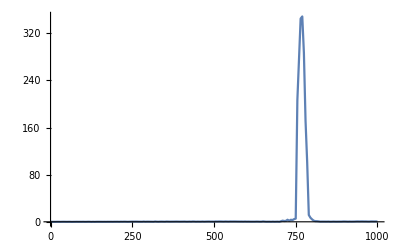

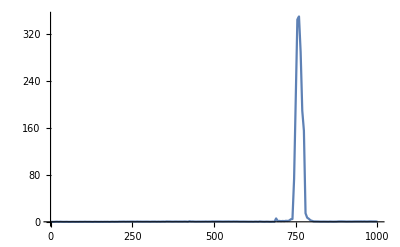

```mathematica
ListLinePlot[{avgProf[[1]]},PlotRange->Full,PlotLegends->labels[[1]]]
ListLinePlot[{avgProf[[2]]},PlotRange->Full,PlotLegends->labels[[2]]]
```

### Compare AVGs

```mathematica
normalize[data_]:=Transpose@{data[[All,1]],Rescale[data[[All,2]]]};

normalize2[data_]:=Module[{xvals,yvals,maxval},xvals=data[[All,1]];
yvals=data[[All,2]];
maxval=Max[yvals];
Transpose@{xvals,yvals/maxval}];

normalize3[data_]:=Module[{xvals,yvals,meanval},xvals=data[[All,1]];
yvals=data[[All,2]];
meanval=Mean[yvals];
Transpose@{xvals,yvals/meanval}];

normalize4[data_]:=Module[{xvals,yvals,refIndex,refVal},xvals=data[[All,1]];
yvals=data[[All,2]];
refIndex=First@FirstPosition[xvals,x_/;Abs[x-600]<10^-3];
refVal=yvals[[refIndex]];
Transpose@{xvals,yvals/refVal}];

normalize5[data_]:=Module[{xvals,yvals,sel,meanval},xvals=data[[All,1]];
yvals=data[[All,2]];
sel=Select[Transpose@{xvals,yvals},400<=#[[1]]<=800&];
meanval=Mean[sel[[All,2]]];
Transpose@{xvals,yvals/meanval}];

nnA=normalize/@avgProf;
nnB=normalize2/@avgProf;
nnC=normalize3/@avgProf;
nnD=normalize4/@avgProf;
nnE=normalize5/@avgProf;
```

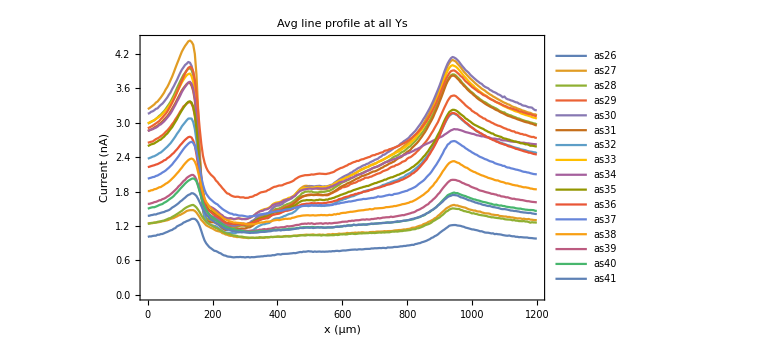
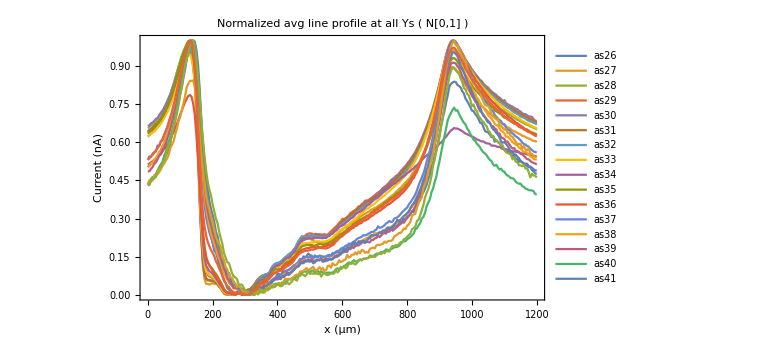
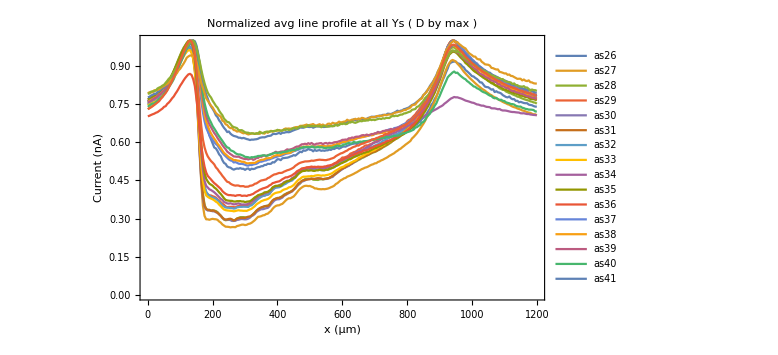
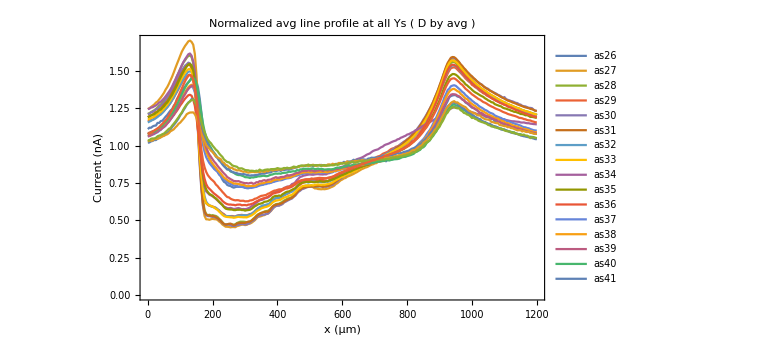
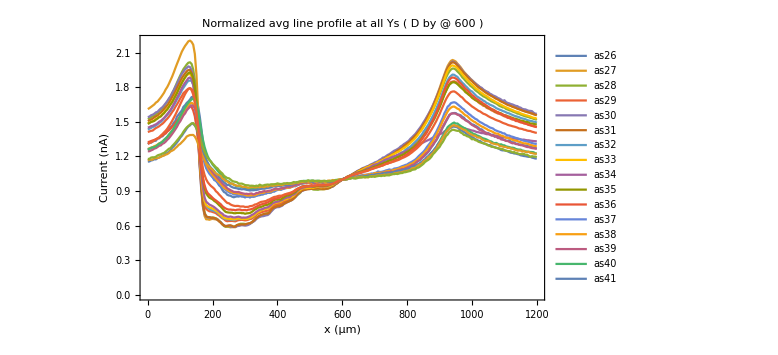
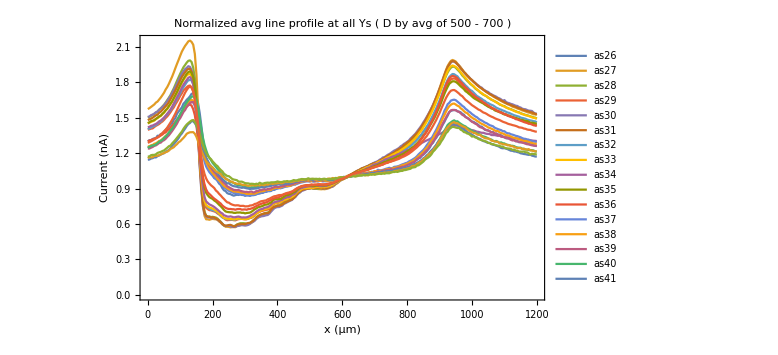

```mathematica
sel={1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19};
pp0=ListLinePlot[avgProf[[#]]&/@sel,PlotRange->Full,PlotLegends->Placed[labels[[#]]&/@sel,Right],
PlotStyle->Automatic,
Frame->True,
FrameLabel->{"x (μm)","Current (nA)"},
PlotLabel->"Avg line profile at all Ys",
LabelStyle->{FontFamily->"Arial",FontSize->14},
ImageSize->Large
];
pp1=ListLinePlot[nnA[[#]]&/@sel,PlotRange->Full,PlotLegends->{labels[[#]]&/@sel},
PlotStyle->Automatic,
Frame->True,
FrameLabel->{"x (μm)","Current (nA)"},
PlotLabel->"Normalized avg line profile at all Ys ( N[0,1] )",
LabelStyle->{FontFamily->"Arial",FontSize->14},
ImageSize->Large
];
pp2=ListLinePlot[nnB[[#]]&/@sel,PlotRange->Full,PlotLegends->{labels[[#]]&/@sel},
PlotStyle->Automatic,
Frame->True,
FrameLabel->{"x (μm)","Current (nA)"},
PlotLabel->"Normalized avg line profile at all Ys ( D by max )",
LabelStyle->{FontFamily->"Arial",FontSize->14},
ImageSize->Large
];
pp3=ListLinePlot[nnC[[#]]&/@sel,PlotRange->Full,PlotLegends->{labels[[#]]&/@sel},
PlotStyle->Automatic,
Frame->True,
FrameLabel->{"x (μm)","Current (nA)"},
PlotLabel->"Normalized avg line profile at all Ys ( D by avg )",
LabelStyle->{FontFamily->"Arial",FontSize->14},
ImageSize->Large
];
pp4=ListLinePlot[nnD[[#]]&/@sel,PlotRange->Full,PlotLegends->{labels[[#]]&/@sel},
PlotStyle->Automatic,
Frame->True,
FrameLabel->{"x (μm)","Current (nA)"},
PlotLabel->"Normalized avg line profile at all Ys ( D by @ 600 )",
LabelStyle->{FontFamily->"Arial",FontSize->14},
ImageSize->Large
];
pp5=ListLinePlot[nnE[[#]]&/@sel,PlotRange->Full,PlotLegends->{labels[[#]]&/@sel},
PlotStyle->Automatic,
Frame->True,
FrameLabel->{"x (μm)","Current (nA)"},
PlotLabel->"Normalized avg line profile at all Ys ( D by avg of 500 - 700 )",
LabelStyle->{FontFamily->"Arial",FontSize->14},
ImageSize->Large
];
{pp0,pp1,pp2,pp3,pp4,pp5}
```

## Export

```mathematica
sel={1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19};
dd0=avgProf[[#]]&/@sel;
dd1=nnA[[#]]&/@sel;
dd2=nnB[[#]]&/@sel;
dd3=nnC[[#]]&/@sel;
dd4=nnD[[#]]&/@sel;
dd5=nnE[[#]]&/@sel;

ddList={dd0,dd1,dd2,dd3,dd4,dd5};
sheetNames={"Raw","Norm01","NormMax","NormAvg","Norm600","Norm500-700"};
headerRow=Prepend[labels[[#]]&/@sel,"x"];

dddList=Table[
Module[{data},
data=Table[
Prepend[
Table[ddList[[k]][[j]][[i,2]],{j,1,Length[sel]}]
,ddList[[k]][[1]][[i,1]]]
,{i,1,nx}];
Prepend[Prepend[data,headerRow],{sheetNames[[k]]}]]
,{k,Length[ddList]}];

Export[filename<>"_avg,norm-profiles.xlsx",dddList]
```

250708-secm1-g1-p5-as26-45_avg,norm-profiles.xlsx

```mathematica
(*
ddd0=Table[
Prepend[Table[dd0[[j]][[i,2]],{j,1,Length[sel]}],dd0[[1]][[i,1]]],
{i,1,nx}];
ddd0//Dimensions;
ddd0//MatrixForm;
Export[filename<>"test.xlsx",ddd0]
*)
```

#### functions for data export and flip

```mathematica
flipXY[data_]:=MapThread[{#1[[1]],#2[[2]]}&,{data,Reverse[data]}];
```

```mathematica
flippedAvg=flipXY/@avgProfiles;
```

```mathematica
ListLinePlot[{flippedAvg[[1]],flippedAvg[[2]]},PlotStyle->Automatic,Frame->True,FrameLabel->{"x (μm)","Current (nA)"},PlotLabel->"avg Line Profile at all y",PlotRange->All,PlotLegends->Placed[{"as12","as13"},Right],
LabelStyle->{FontFamily->"Arial",FontSize->14},ImageSize->Large];
```

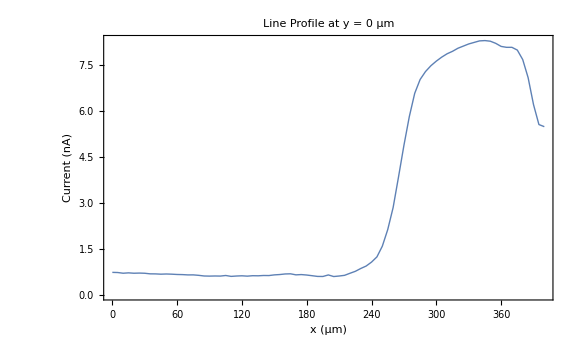

{81,2}

```mathematica
LPy[0]
data0=GetLPyRData[0];
data0//TableForm;
data0//Dimensions
```

```mathematica
t0=GetLPyRData[0];
t2=GetLPyRData[20];
t4=GetLPyRData[40];
t0//Dimensions
```

{81,2}

```mathematica
ttt={t0,t2,t4};
ttt//Dimensions
Export[filename<>"0-40.xlsx",ttt]
```

{3,81,2}

5_10_as0-40.xlsx

## --------later-----

#### Spike correction (need update, deactivated)

```mathematica
"ClearAll[getZ];
getZ[x_,y_]:=Module[{xi,yi},
xi=Round[x/dx]+1;
yi=Round[y/dy]+1;
];
```

```mathematica
"ClearAll[setZ];
setZ[x_,y_,newVal_]:=Module[{xi,yi},
xi=Round[x/dx]+1;
yi=Round[y/dy]+1;
];
```

```mathematica
"ClearAll[SmoothZSpike];
SmoothZSpike[xStart_,xEnd_,y_,noiseAmp_:0.05]:=Module[{xiStart,xiEnd,yi,z1,z2,n,xs,linFit,noise,newVals},(*Index conversion*)xiStart=Round[xStart/dx]+1;
xiEnd=Round[xEnd/dx]+1;
yi=Round[y/dy]+1;
(*Length and original endpoints*)
n=xiEnd-xiStart+1;
z1=zMatrix[[yi,xiStart]];
z2=zMatrix[[yi,xiEnd]];
(*X-index vector*)
xs=Range[0,n-1];
(*Linear interpolation+small noise*)
linFit=z1+(z2-z1)*(xs/(n-1));
noise=RandomReal[{-noiseAmp,noiseAmp},n];
newVals=linFit+noise;
(*Apply correction*)
Do[zMatrix[[yi,xiStart+i-1]]=newVals[[i]],{i,1,n}];
(*Return updated profile for review*)
newVals];
```

### b. Correction 1 (optional, need update)

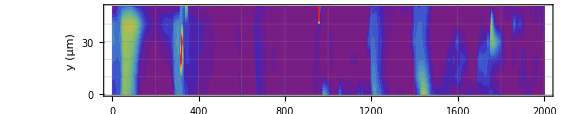

```mathematica
map[zMatrix,0.1,4,20]
```

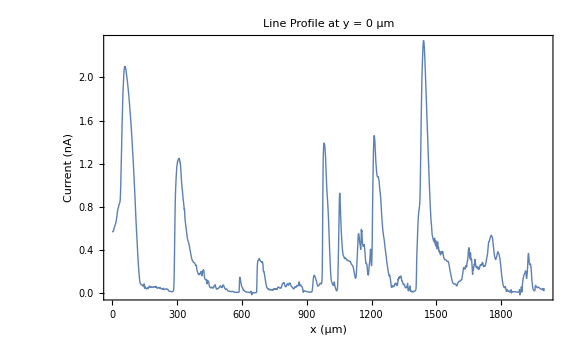

```mathematica
LPy[0]
```

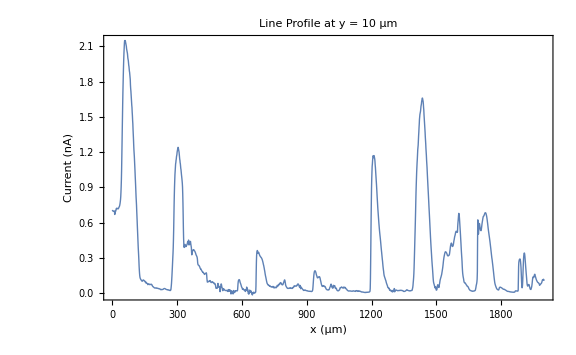

```mathematica
LPy[10]
```

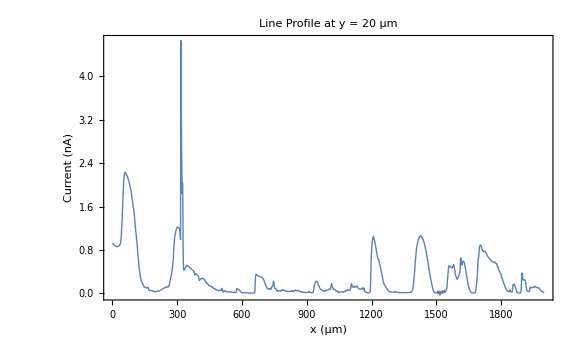

```mathematica
LPy[20]
```

```mathematica
Table[getZ[x,20],{x,310,340,1}]
```

{1.2,1.19,1.17,1.14,1.1,1.04,0.992,4.66,4.47,3.63,3.01,2.61,2.25,1.84,1.97,2.03,1.97,1.43,0.777,0.531,0.465,0.431,0.424,0.429,0.438,0.445,0.453,0.46,0.468,0.475,0.485}

```mathematica
Table[getZ[x,20],{x,316,328,1}]
```

{0.992,4.66,4.47,3.63,3.01,2.61,2.25,1.84,1.97,2.03,1.97,1.43,0.777}

```mathematica
SmoothZSpike[316,328,20]
```

{1.01926,1.01683,0.92821,0.968952,0.876188,0.904426,0.893926,0.91209,0.824584,0.867157,0.80053,0.750722,0.80336}

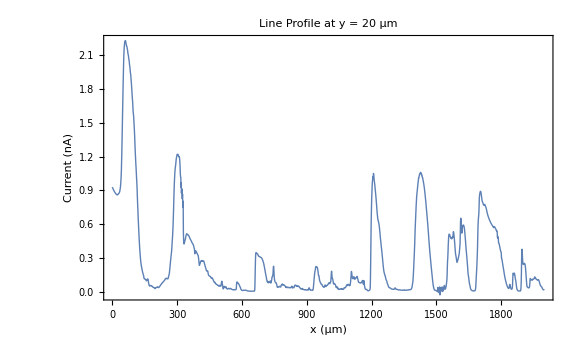

```mathematica
LPy[20]
```

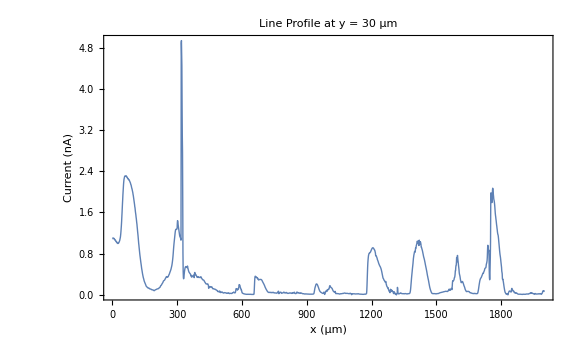

```mathematica
LPy[30]
```

```mathematica
Table[getZ[x,30],{x,300,340,1}]
```

{1.29,1.39,1.44,1.42,1.39,1.35,1.32,1.29,1.26,1.23,1.2,1.17,1.14,1.13,1.12,1.11,1.1,1.07,1.06,4.89,4.94,4.68,4.45,3.67,3.08,2.77,1.85,0.82,0.455,0.334,0.309,0.326,0.364,0.408,0.448,0.477,0.503,0.522,0.536,0.543,0.547}

```mathematica
Table[getZ[x,30],{x,318,327,1}]
```

{1.06,4.89,4.94,4.68,4.45,3.67,3.08,2.77,1.85,0.82}

```mathematica
SmoothZSpike[318,327,30]
```

{1.05896,1.07103,1.04823,0.994448,0.920252,0.940584,0.923995,0.85056,0.857712,0.797197}

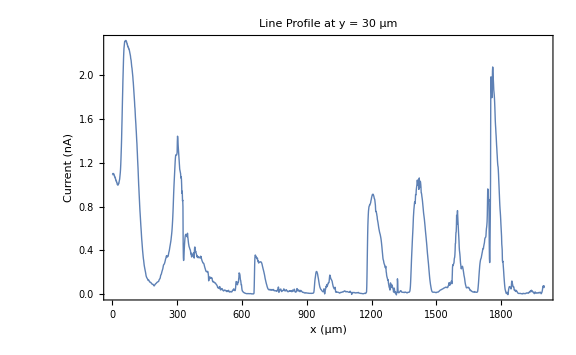

```mathematica
LPy[30]
```

```mathematica
Table[getZ[x,30],{x,1720,1810,1}]
```

{0.444,0.455,0.464,0.475,0.497,0.509,0.515,0.517,0.52,0.523,0.54,0.575,0.6,0.612,0.633,0.66,0.722,0.842,0.96,0.957,0.922,0.883,0.845,0.864,0.749,0.476,0.324,0.29,0.326,0.537,0.729,1.03,1.81,1.98,1.96,1.9,1.84,1.79,1.8,1.91,2.03,2.07,2.05,2.,1.95,1.91,1.86,1.84,1.82,1.79,1.75,1.7,1.64,1.58,1.54,1.51,1.47,1.44,1.4,1.36,1.33,1.29,1.26,1.22,1.19,1.17,1.16,1.13,1.09,1.04,0.997,0.95,0.903,0.854,0.812,0.778,0.751,0.722,0.685,0.642,0.604,0.567,0.528,0.459,0.434,0.405,0.31,0.295,0.302,0.285,0.258}

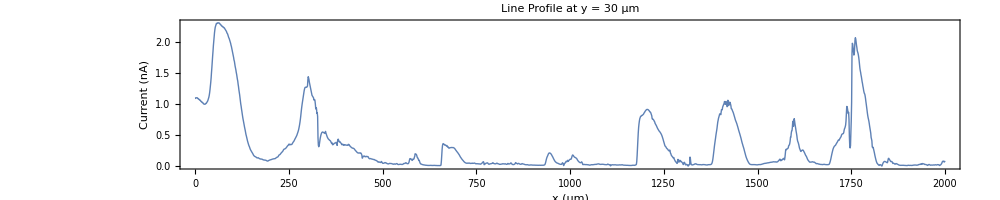

-Graphics-

```mathematica
LPy2[y_]:=Module[{rowIndex,xvals,lineProfile},
rowIndex=Round[y/dy]+1;
If[rowIndex<1||rowIndex>ny,Return["Error: y = "<>ToString[y]<>" µm is out of range."]];
xvals=Range[0,dx*(nx-1),dx];
lineProfile=zMatrix[[rowIndex]];
ListLinePlot[Transpose[{xvals,lineProfile}],Frame->True,FrameLabel->{"x (μm)","Current (nA)"},PlotLabel->"Line Profile at y = "<>ToString[y]<>" μm",PlotRange->All,PlotStyle->Thick,LabelStyle->{FontFamily->"Arial",FontSize->14},ImageSize->1000,AspectRatio->1/5]];
LPy2[30]
LPy[30]
```

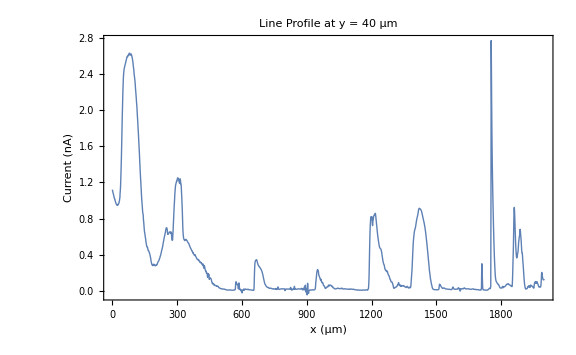

```mathematica
LPy[40]
```

```mathematica
Table[getZ[x,40],{x,1753,1767,1}]
```

{0.978,2.77,2.49,2.13,1.84,1.61,1.42,1.27,1.13,1.01,0.897,0.791,0.691,0.6,0.515}

```mathematica
SmoothZSpike[1753,1767,40]
```

{0.952613,0.975778,0.925963,0.864823,0.891332,0.859434,0.778226,0.721815,0.751053,0.713638,0.6659,0.637511,0.53385,0.540674,0.561383}

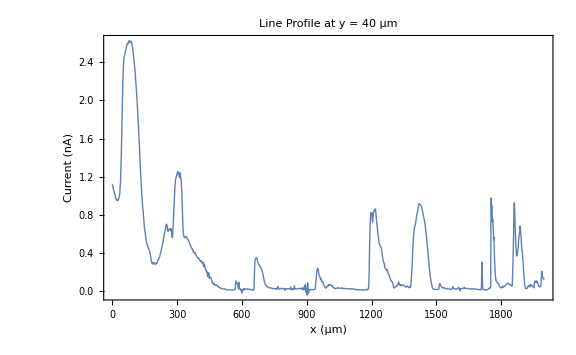

```mathematica
LPy[40]
```

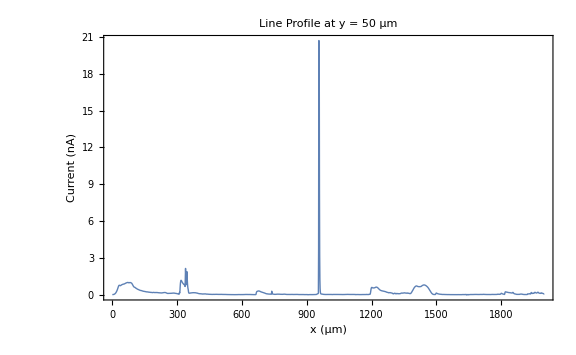

```mathematica
LPy[50]
```

{0.134,3.71,20.7,20.7,19.6,8.56,3.24,1.25,0.513,0.233,0.124,0.0837,0.0685}

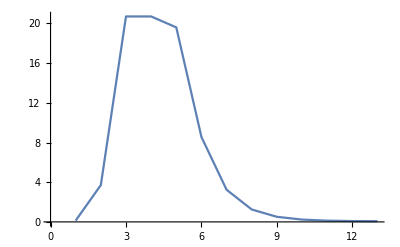

```mathematica
Table[getZ[x,50],{x,954,966,1}]
ListLinePlot[Table[getZ[x,50],{x,954,966,1}]]
```

```mathematica
SmoothZSpike[954,966,50]
```

{0.104697,0.0854405,0.167126,0.0841441,0.130825,0.0739701,0.150315,0.0686074,0.0409364,0.105628,0.10504,0.0886731,0.0863774}

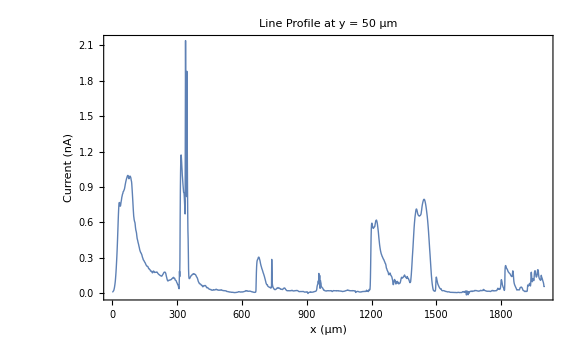

```mathematica
LPy[50]
```

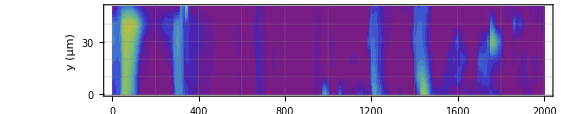

```mathematica
map[zMatrix,0.1,4,20]
```

### c. Correction 2 (optional, need update)

```mathematica
map[zMatrix,0.1,4,20]
```

-Graphics-

```mathematica
{LPy[20],LPy[30],LPy[40]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[getZ[x,30],{x,1730,1800,1}]
```

{0.54,0.575,0.6,0.612,0.633,0.66,0.722,0.842,0.96,0.957,0.922,0.883,0.845,0.864,0.749,0.476,0.324,0.29,0.326,0.537,0.729,1.03,1.81,1.98,1.96,1.9,1.84,1.79,1.8,1.91,2.03,2.07,2.05,2.,1.95,1.91,1.86,1.84,1.82,1.79,1.75,1.7,1.64,1.58,1.54,1.51,1.47,1.44,1.4,1.36,1.33,1.29,1.26,1.22,1.19,1.17,1.16,1.13,1.09,1.04,0.997,0.95,0.903,0.854,0.812,0.778,0.751,0.722,0.685,0.642,0.604}

```mathematica
Table[getZ[x,30],{x,1735,1747,1}]
```

{0.66,0.722,0.842,0.96,0.957,0.922,0.883,0.845,0.864,0.749,0.476,0.324,0.29}

```mathematica
Table[getZ[x,30],{x,1748,1759,1}]
```

{0.326,0.537,0.729,1.03,1.81,1.98,1.96,1.9,1.84,1.79,1.8,1.91}

```mathematica
SmoothZSpike[1735,1747,30]
SmoothZSpike[1748,1759,30]
```

{0.703145,0.654914,0.559953,0.527362,0.574504,0.550119,0.520043,0.484046,0.453086,0.339134,0.32463,0.323315,0.321565}

{0.293841,0.454135,0.629223,0.720145,0.857644,0.99977,1.19685,1.36378,1.44099,1.65163,1.73197,1.95515}

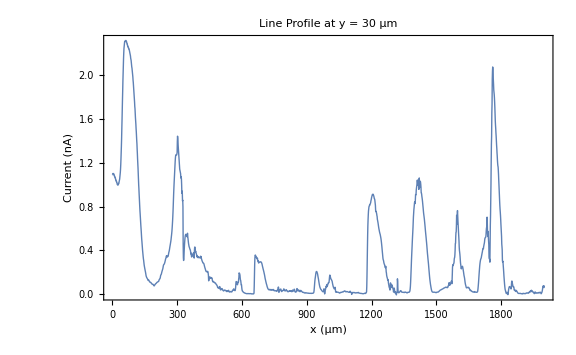

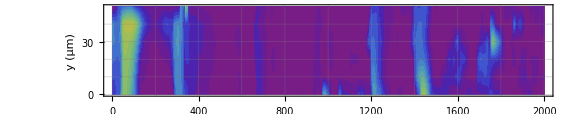

```mathematica
LPy[30]
map[zMatrix,0.1,4,20]
```

```mathematica
LPy[50]
```

-Graphics-

```mathematica
Table[getZ[x,50],{x,300,400,1}]
```

{0.0856,0.0818,0.0755,0.0704,0.0685,0.066,0.0578,0.0471,0.0401,0.0376,0.105,0.185,0.14,0.281,0.616,0.871,1.03,1.13,1.17,1.17,1.14,1.11,1.07,1.04,1.,0.976,0.949,0.923,0.9,0.877,0.854,0.851,0.849,0.821,0.782,0.745,0.708,0.671,1.45,2.14,1.66,1.31,1.09,0.928,0.818,1.88,1.62,1.25,0.912,0.686,0.532,0.46,0.341,0.201,0.147,0.128,0.123,0.123,0.125,0.127,0.13,0.136,0.139,0.142,0.146,0.148,0.149,0.149,0.152,0.155,0.158,0.159,0.16,0.161,0.163,0.164,0.165,0.163,0.161,0.161,0.163,0.161,0.16,0.159,0.158,0.157,0.154,0.15,0.147,0.142,0.138,0.136,0.134,0.13,0.125,0.12,0.114,0.106,0.1,0.0957,0.0925}

```mathematica
Table[getZ[x,50],{x,334,344,1}]
```

{0.782,0.745,0.708,0.671,1.45,2.14,1.66,1.31,1.09,0.928,0.818}

```mathematica
SmoothZSpike[334,344,50]
```

{0.800071,0.753509,0.837532,0.830961,0.774267,0.756094,0.777145,0.80103,0.804482,0.833532,0.817467}

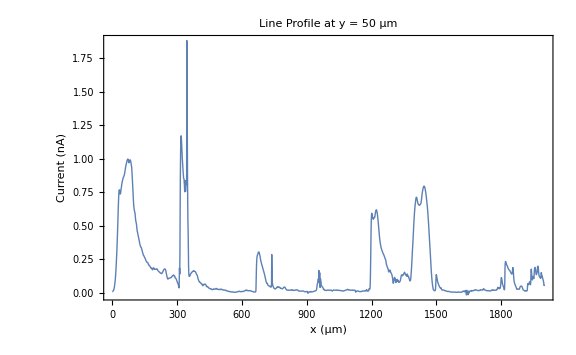

```mathematica
LPy[50]
```

```mathematica
Table[getZ[x,50],{x,341,351,1}]
```

{0.80103,0.804482,0.833532,0.817467,1.88,1.62,1.25,0.912,0.686,0.532,0.46}

```mathematica
SmoothZSpike[341,351,50]
```

{0.840395,0.762747,0.772371,0.657224,0.68048,0.611963,0.63335,0.524009,0.524712,0.515163,0.472781}

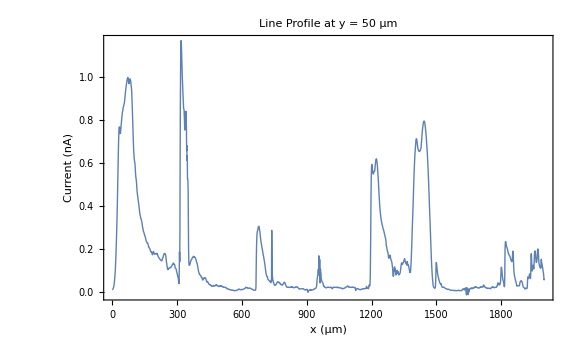

```mathematica
LPy[50]
```

## Final?

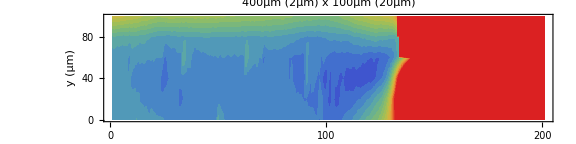

```mathematica
map[zMatrix,0.1,2,20]
```

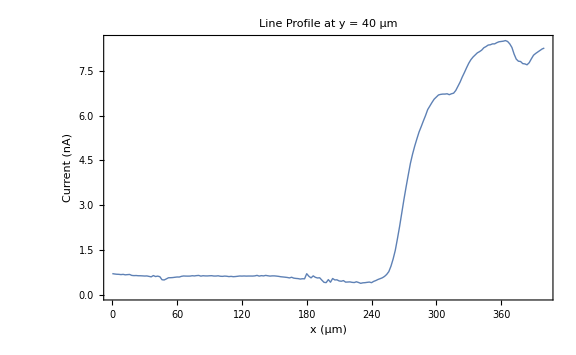

```mathematica
LPy[40]
```

## Final touch-flip

```mathematica
zMatrixR=Map[Reverse,zMatrix];
```

```mathematica
ClearAll[LPy];
LPyR[y_]:=Module[{rowIndex,xvals,lineProfile},
rowIndex=Round[y/dy]+1;
If[rowIndex<1||rowIndex>ny,Return["Error: y = "<>ToString[y]<>" µm is out of range."]];
xvals=Range[0,dx*(nx-1),dx];
lineProfile=zMatrixR[[rowIndex]];
ListLinePlot[Transpose[{xvals,lineProfile}],Frame->True,FrameLabel->{"x (μm)","Current (nA)"},PlotLabel->"Line Profile at y = "<>ToString[y]<>" μm",PlotRange->All,PlotStyle->Thick,LabelStyle->{FontFamily->"Arial",FontSize->14},ImageSize->Large]];
```

```mathematica
GetLPyRData[y_]:=Module[{rowIndex,xvals,lineProfile},rowIndex=Round[y/dy]+1;
If[rowIndex<1||rowIndex>ny,Return["Error: y = "<>ToString[y]<>" µm is out of range."]];
xvals=Range[0,dx*(nx-1),dx];
lineProfile=zMatrixR[[rowIndex]];
Transpose[{xvals,lineProfile}]];
```

```mathematica
map[zMatrixR,0.1,3,20]
```

-Graphics-

```mathematica
LPyR[10]
```

-Graphics-

```mathematica
data10=GetLPyRData[10];
ListLinePlot[data10,PlotRange->All]
Export["LPyR_10.csv",data10]
```

-Graphics-

LPyR_10.csv

```mathematica
LPyR[30]
```

-Graphics-

```mathematica
avgProfile=Mean[zMatrixR];
xvals=Range[0,dx*(nx-1),dx];
ListLinePlot[Transpose[{xvals,avgProfile}],PlotRange->All,Frame->True,FrameLabel->{"x (μm)","Averaged Current (nA)"},PlotLabel->"Averaged Line Profile (Y = 0–50 μm)",PlotStyle->Thick,LabelStyle->{FontFamily->"Arial",FontSize->14},ImageSize->Large]
```

-Graphics-

```mathematica
xvals//Dimensions;
dataavg={xvals,avgProfile};
dataavg//Dimensions
ListLinePlot[Transpose[dataavg],PlotRange->All]
Export["data_avg.csv",dataavg]
```

{2,2001}

-Graphics-

data_avg.csv

```mathematica
avgProfile2=Mean[zMatrixR[[{2,3,4}]]];
xvals=Range[0,dx*(nx-1),dx];
ListLinePlot[Transpose[{xvals,avgProfile2}],PlotRange->All,Frame->True,FrameLabel->{"x (μm)","Averaged Current (nA)"},PlotLabel->"Averaged Profile at y = 0, 10, 20 μm",PlotStyle->Thick,LabelStyle->{FontFamily->"Arial",FontSize->14},ImageSize->Large]
```

-Graphics-

```mathematica
LPyR[40]
```

-Graphics-